```mathematica
ψ={0.8479137837388718,
0.5972483318258885,
0.20590311426874863,
0.15626245943631073,
2.5800377269010863,
0.5191602991363214,
2.219593967401592,
0.26026881300451354,
9.05693877847928,
9.600156007610929,
0.16113962322340247,
0.6882242167021784,
0.9043834668391743,
5.366184617021723,
0.09453876907781399,
1.3946897293830476};
```

```mathematica
ζν0=(4+Sqrt[816])/400;
```

```mathematica
αν0=4*ζν0+1;
```

```mathematica
η1 = Total[Log[ψ]-ψ]-2ζν0
```

-37.3692

```mathematica
T=16;
```

```mathematica
lpν[ν_]:= (T*ν/2+αν0-1)*Log[ν/2]-T*LogGamma[ν/2]+ν/2*η1
```

```mathematica
νmin=0.0;
```

```mathematica
νmax=500;
```

```mathematica
NIntegrate[Exp[lpν[ν]]*ν,{ν,νmin,νmax}]/NIntegrate[Exp[lpν[ν]],{ν,νmin,νmax}]
```

1.0728

```mathematica
NumberForm[1.0728001734671155,16]
```

1.072800173467116

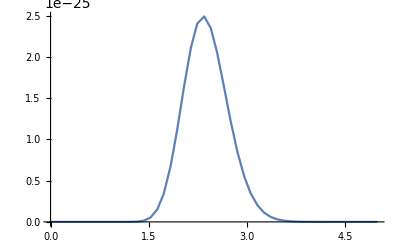

```mathematica
Plot[Exp[lpν[ν]],{ν,0.0,5.0}]
```

```mathematica
NIntegrate[ν*Exp[lpν[ν]],{ν,νmin,νmax},AccuracyGoal-> 50]/NIntegrate[Exp[lpν[ν]],{ν,νmin,νmax},AccuracyGoal-> 50]
```

0.972621

```mathematica
NumberForm[0.97262064511702,16]
```

0.97262064511702

```mathematica
NumberForm[0.9726206451297836,16]
```

0.972620645129784

```mathematica
NIntegrate[PDF[GammaDistribution[0.08,1/0.02],x]x,{x,νmin,νmax},MaxRecursion->100]
```

4.

```mathematica
1-0.07970505574341707
```

```mathematica
NIntegrate[PDF[GammaDistribution[0.08,1/0.02],x]x,{x,1,80},MaxRecursion->100]
```

3.03972

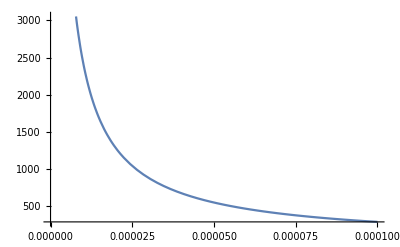

```mathematica
Plot[PDF[GammaDistribution[0.08,1/0.02],x],{x,0,.0001}]
```